# Networks Visualization and Data Analysis

HMSC :: Routines for the display of animations and iterated experiments on networks epidemics

## Definitions

## Import Stuff

```mathematica
<<PajaroLocoPublic`
SetDirectory[NotebookDirectory[]]
GraphIntoEdgesList[randomGraph_]:=Module[{adjacencyMatrix,verticesNames,edgesList},
adjacencyMatrix=randomGraph//AdjacencyMatrix;
verticesNames=ToString/@Range[adjacencyMatrix//Length];
edgesList=ConvertAdjacencyMatrixToEdgesList[{adjacencyMatrix,verticesNames},AllowLoops->False]
]
```

/Users/chipdelmal/Documents/School/Research/googleNetworks/temporalGillespie/Animations

## Mods

```mathematica
<<PajaroLoco`
Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]

VertexNumberToVertexSyllable[syllables_,fixedEdgesList_]:=Table[DirectedEdge[syllables[[fixedEdgesList[[index]][[1]][[1]]]],syllables[[fixedEdgesList[[index]][[1]][[2]]]]->fixedEdgesList[[index]][[2]]]//N,{index,1,Length[fixedEdgesList]}]
Options[GraphTransitionsFrequenciesWithMax]:={VertexCoordinates->Automatic,LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic}}
edgeshape[e_,___]:={Arrowheads[{{.015,.9}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,EdgeStyle->edgesStyleList,ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexStyle->Directive[White,EdgeForm[None]],VertexLabelStyle->OptionValue[VertexLabelStyle],VertexCoordinates->OptionValue[VertexCoordinates],VertexLabels->Placed["Name",Center],EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}]]]
```

GetPackageVersion::shdw: Symbol GetPackageVersion appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

ExtractTimedSyllablesFromTextGrid::shdw: Symbol ExtractTimedSyllablesFromTextGrid appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

DeletePhraseIfLonger::shdw: Symbol DeletePhraseIfLonger appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

SplitSongWherePhraseCountIsLower::shdw: Symbol SplitSongWherePhraseCountIsLower appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

ImportSongFromTextGrid::shdw: Symbol ImportSongFromTextGrid appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetPhrasesFrequencies::shdw: Symbol GetPhrasesFrequencies appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetPhrasesFrequenciesWithPattern::shdw: Symbol GetPhrasesFrequenciesWithPattern appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetPhrasesCumulativeFrequencies::shdw: Symbol GetPhrasesCumulativeFrequencies appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetPhrasesCumulativeFrequenciesWithPattern::shdw: Symbol GetPhrasesCumulativeFrequenciesWithPattern appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

BarChartPhrasesFrequencies::shdw: Symbol BarChartPhrasesFrequencies appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

BarChartPhrasesCumulativeFrequencies::shdw: Symbol BarChartPhrasesCumulativeFrequencies appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

ListPlotSong::shdw: Symbol ListPlotSong appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

PlotScaledSongWithFrequency::shdw: Symbol PlotScaledSongWithFrequency appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

LogLogPlotPhrasesFrequencies::shdw: Symbol LogLogPlotPhrasesFrequencies appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetZipfModelFromPhrasesFrequencies::shdw: Symbol GetZipfModelFromPhrasesFrequencies appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetCumulativeNumberOfDifferentPhrases::shdw: Symbol GetCumulativeNumberOfDifferentPhrases appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

PlotCumulativeNumberOfDifferentPhrases::shdw: Symbol PlotCumulativeNumberOfDifferentPhrases appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetRepertoire::shdw: Symbol GetRepertoire appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetRepertoireSize::shdw: Symbol GetRepertoireSize appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetWindowedRepertoire::shdw: Symbol GetWindowedRepertoire appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetWindowedRepertoireSize::shdw: Symbol GetWindowedRepertoireSize appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

PlotWindowedRepertoireSize::shdw: Symbol PlotWindowedRepertoireSize appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetCumulativeRepertoire::shdw: Symbol GetCumulativeRepertoire appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetPairwiseRepertoireSimilarity::shdw: Symbol GetPairwiseRepertoireSimilarity appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetTransitionsMarkov::shdw: Symbol GetTransitionsMarkov appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetTransitionsMarkovWithPattern::shdw: Symbol GetTransitionsMarkovWithPattern appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetTransitionsFrequencies::shdw: Symbol GetTransitionsFrequencies appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetTransitionsFrequenciesWithPattern::shdw: Symbol GetTransitionsFrequenciesWithPattern appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

TableFormTransitions::shdw: Symbol TableFormTransitions appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GraphTransitionsMarkov::shdw: Symbol GraphTransitionsMarkov appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GraphTransitionsFrequencies::shdw: Symbol GraphTransitionsFrequencies appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GridColorScaleMarkov::shdw: Symbol GridColorScaleMarkov appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GridColorScaleFrequency::shdw: Symbol GridColorScaleFrequency appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

ConvertAdjacencyMatrixToEdgesList::shdw: Symbol ConvertAdjacencyMatrixToEdgesList appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GraphCentrality::shdw: Symbol GraphCentrality appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GraphCommunities::shdw: Symbol GraphCommunities appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

PlotDegreeDistribution::shdw: Symbol PlotDegreeDistribution appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetSmallWorldCoefficient::shdw: Symbol GetSmallWorldCoefficient appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

TableFormCommunities::shdw: Symbol TableFormCommunities appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetCommunitiesInOutTransitionsFrequencies::shdw: Symbol GetCommunitiesInOutTransitionsFrequencies appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetCommunitiesInOutTransitionsRatios::shdw: Symbol GetCommunitiesInOutTransitionsRatios appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetCommunitiesInOutTransitionsGlobalRatio::shdw: Symbol GetCommunitiesInOutTransitionsGlobalRatio appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

ListPlotSongWithCommunities::shdw: Symbol ListPlotSongWithCommunities appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

TestScripts::shdw: Symbol TestScripts appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

RunCollocationsScript::shdw: Symbol RunCollocationsScript appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

RunNewmanScript::shdw: Symbol RunNewmanScript appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

RunAlignmentScript::shdw: Symbol RunAlignmentScript appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GridAlignment::shdw: Symbol GridAlignment appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

ConvertEdgesListToAdjacencyMatrix::shdw: Symbol ConvertEdgesListToAdjacencyMatrix appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

ConvertCollocationsFrequenciesToCoOccurrencesAdjacencyMatrix::shdw: Symbol ConvertCollocationsFrequenciesToCoOccurrencesAdjacencyMatrix appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

ConvertCollocationsFrequenciesToCoOccurrencesAdjacencyMatrixWithPattern::shdw: Symbol ConvertCollocationsFrequenciesToCoOccurrencesAdjacencyMatrixWithPattern appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

ConvertAdjacencyMatrixToiGraphEdgeList::shdw: Symbol ConvertAdjacencyMatrixToiGraphEdgeList appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

ExportAdjacencyMatrixToNCol::shdw: Symbol ExportAdjacencyMatrixToNCol appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

ImportGraphFromNColFile::shdw: Symbol ImportGraphFromNColFile appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

ImportGraphFromNColWithPhrasesLabels::shdw: Symbol ImportGraphFromNColWithPhrasesLabels appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

MatrixPlotSong::shdw: Symbol MatrixPlotSong appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetTransitionsGraph::shdw: Symbol GetTransitionsGraph appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetColocationsGraph::shdw: Symbol GetColocationsGraph appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetTransitionsGraphWithPattern::shdw: Symbol GetTransitionsGraphWithPattern appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetColocationsGraphWithPattern::shdw: Symbol GetColocationsGraphWithPattern appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetIndividualTransitionsGraph::shdw: Symbol GetIndividualTransitionsGraph appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetIndividualColocationsGraph::shdw: Symbol GetIndividualColocationsGraph appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetIndividualTransitionsGraphWithPattern::shdw: Symbol GetIndividualTransitionsGraphWithPattern appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GetIndividualColocationsGraphWithPattern::shdw: Symbol GetIndividualColocationsGraphWithPattern appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

GraphTransitionsFrequenciesWithMax::shdw: Symbol GraphTransitionsFrequenciesWithMax appears in multiple contexts {PajaroLoco`,PajaroLocoPublic`}; definitions in context PajaroLoco` may shadow or be shadowed by other definitions.

## PlotStyleDefinition

```mathematica
Themes`AddThemeRules["ChipdelmalTheme",
DefaultPlotStyle->Thread@Directive[ColorData[1,"ColorList"],Thickness[.01]],
LabelStyle->Directive[Black,30],
AxesStyle->White,
Frame->True,
FrameTicksStyle->Directive[Black,15],
FrameStyle->Directive[Black,Thick],
GridLines->Automatic,
GridLinesStyle->Directive[Black,Thin,Dashed],
TicksStyle->LightGray,
Background->White
]
Themes`AddThemeRules["ChipdelmalDarkTheme",
DefaultPlotStyle->Thread@Directive[ColorData[59,"ColorList"],Thickness[.01]],
Frame->True,
FrameStyle->Black,
FrameTicksStyle->Directive[Black,15],
LabelStyle->Directive[Black,30],
Prolog->{Black,Opacity[1],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],Dashed,White],Method->{"GridLinesInFront"->True}
]
```

ChipdelmalTheme

ChipdelmalDarkTheme

## Functions

```mathematica
GenerateSIRTriplets[rawData_]:=Module[{time,sir,triplets},
time=rawData[[All,4]];
sir=rawData[[All,1;;3]];
triplets=Transpose[{time,#}]&/@Transpose[sir]
]
GetSIRRawData[fileName_]:=Import[fileName][[2;;All]][[All,2;;All]]
InterpolateSIRFunctions[triplets_]:=Module[{sirFunctions},
Clear[t];
sirFunctions=Interpolation[#,InterpolationOrder->0]&/@triplets;
(#[t]&/@sirFunctions)
]
InterpolateSIRFunctionsFromData[fileName_]:=Module[{rawData,triplets,func},
rawData=GetSIRRawData[fileName];
triplets=GenerateSIRTriplets[rawData];
func=InterpolateSIRFunctions[triplets]
]
CalculateSIRQuartiles[dataset_,{tMin_,tMax_}]:=Module[{evaluation},
Table[
evaluation=Table[dataset[[All,i]]//Quiet,{t,tMin,tMax}];
Transpose[Quartiles/@evaluation]
,{i,1,Length[dataset[[1]]]}]
]
PlotQuartiles[quartiles_,colours_]:=Module[{plot,swatch},
plot=Show[
ListLinePlot[#[[1]],PlotRange->All,PlotStyle->{{#[[2]],Thin},{#[[2]],Thickness[.005]},{#[[2]],Thin}},Filling->{1->{3}}]&/@Transpose[{quartiles,colours}]
,GridLines->Automatic
,GridLinesStyle->Directive[{Gray,Thickness[.0015]}]
,BaseStyle->40
,Frame->True
,FrameStyle->Directive[{Gray,Thickness[.0025]}]
,FrameLabel->(Style[#,40]&/@{"Time","Persons"})
,ImageSize->1000
];
swatch=SwatchLegend[
colours,
Style[#,40,Gray]&/@{"S","I","R"}
];
Grid[{{plot,swatch}}]
]
Options[GraphTransitionsFrequenciesWithMax]:={VertexCoordinates->Automatic,LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},VertexStyle->Automatic,BaseStyle->Automatic,EdgeStyle->Automatic}
edgeshape[e_,___]:={Arrowheads[{{.015,.9}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=UndirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,EdgeStyle->OptionValue[EdgeStyle](*edgesStyleList*),ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexStyle->OptionValue[VertexStyle],VertexLabelStyle->OptionValue[VertexLabelStyle],VertexCoordinates->OptionValue[VertexCoordinates],VertexLabels->Placed["Name",Center],BaseStyle->OptionValue[BaseStyle],EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}]]]
SetDirectory[NotebookDirectory[]]

CreateColorList[scaledHistoryEvent_,max_,colours_]:=Module[{initial,mid,tempReplacement,last},
initial=ConstantArray[scaledHistoryEvent[[1]]->colours[[1]],max];
tempReplacement={Range[scaledHistoryEvent[[2]],scaledHistoryEvent[[3]]],ConstantArray[colours[[2]],1+scaledHistoryEvent[[3]]-scaledHistoryEvent[[2]]]}//Transpose;
mid=ReplacePart[initial,(#[[1]]->(scaledHistoryEvent[[1]]->#[[2]]))&/@tempReplacement];
tempReplacement={Range[scaledHistoryEvent[[3]],max],ConstantArray[colours[[3]],1+max-scaledHistoryEvent[[3]]]}//Transpose;
last=ReplacePart[mid,(#[[1]]->(scaledHistoryEvent[[1]]->#[[2]]))&/@tempReplacement]
]
ImportHistory[fileName_,timeScaling_,NAValue_]:=Module[{rawHistory,scaledHistory,sortedEvents,NA},
Clear[NA];
rawHistory=ToExpression/@Import[fileName][[All,2;;All]][[2;;All]];
rawHistory={#[[1]],#[[2]],#[[3]],If[!IntegerQ[#[[4]]],"X",#[[4]]]}&/@rawHistory;
scaledHistory={#[[1]],#[[2]]*timeScaling//Round,#[[3]]*timeScaling//Round,#[[4]]}&/@rawHistory;
scaledHistory={#[[1]],If[IntegerQ[#[[2]]],#[[2]],NAValue*timeScaling],If[IntegerQ[#[[3]]],#[[3]],NAValue*timeScaling],#[[4]]}&/@scaledHistory;
sortedEvents=Flatten[{scaledHistory[[All,2]],scaledHistory[[All,3]]}]//Sort;

(*Print[scaledHistory];*)
{scaledHistory,sortedEvents}
]
CreateFramesColorList[scaledHistory_,sortedEvents_,colours_]:=Transpose[CreateColorList[#,sortedEvents//Max,colours]&/@scaledHistory]
CreateColorEdgesList[scaledHistoryEvent_,max_,colours_]:=Module[{initial,mid,tempReplacement,last},
initial=ConstantArray[ToString[scaledHistoryEvent[[1]]]<->ToString[scaledHistoryEvent[[4]]]->colours[[1]],max];
tempReplacement={
Range[scaledHistoryEvent[[2]],max],
ConstantArray[ToString[scaledHistoryEvent[[1]]]<->ToString[scaledHistoryEvent[[4]]]->colours[[2]],1+max-scaledHistoryEvent[[2]]]
}//Transpose;
mid=ReplacePart[initial,(#[[1]]->(#[[2]]))&/@tempReplacement]
]
CreateFramesEdgeColorList[scaledHistory_,sortedEvents_,colours_]:=DeleteCases[#,_<->"X"->_]&/@Transpose[CreateColorEdgesList[#,sortedEvents//Max,colours]&/@scaledHistory]
```

/Users/chipdelmal/Documents/School/Research/googleNetworks/temporalGillespie/Animations

```mathematica
GraphIntoEdgesList[randomGraph_]:=Module[{adjacencyMatrix,verticesNames,edgesList},
adjacencyMatrix=randomGraph//AdjacencyMatrix;
verticesNames=ToString/@Range[adjacencyMatrix//Length];
edgesList=ConvertAdjacencyMatrixToEdgesList[{adjacencyMatrix,verticesNames},AllowLoops->False]
]
```

## Routines

## Routines

### Single File

```mathematica
SetDirectory[NotebookDirectory[]];
func=InterpolateSIRFunctionsFromData[NotebookDirectory[]<>"/Dataset/data.csv"];
Plot[func,{t,1,100},PlotTheme->"ChipdelmalTheme"]
```

-Graphics-

### Dataset

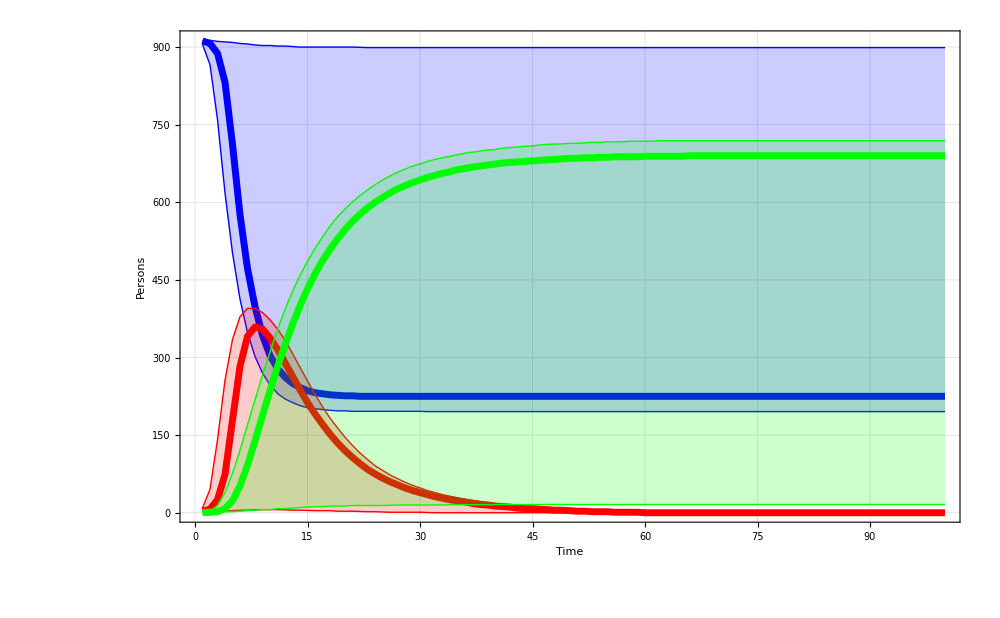
-Graphics- |

TwitterSIR.png

```mathematica
{tMin,tMax}={1,100};
fileNames=FileNames["*.csv",{NotebookDirectory[]<>"/TwitterRandomised"}];
dataset=ParallelMap[InterpolateSIRFunctionsFromData[#]&,fileNames];
quartiles=CalculateSIRQuartiles[dataset, {tMin,tMax}];
PlotQuartiles[quartiles,{Blue,Red,Green}]
Export["TwitterSIR.png",%]
```

## Grids

### Barabasi

```mathematica
{tMin,tMax}={1,80};
fileNames=FileNames["*.csv",{NotebookDirectory[]<>"/Barabasi"}];
dataset=ParallelMap[InterpolateSIRFunctionsFromData[#]&,fileNames];
quartiles=CalculateSIRQuartiles[dataset, {tMin,tMax}];
quartilesBarabasi=PlotQuartiles[quartiles,{Blue,Red,Green}];
```

```mathematica
rawData={#[[1]],#[[2]],1}&/@Import["Barabasi.csv"];
edges=Flatten[{ToString[#[[1]]]->ToString[#[[2]]]}&/@Transpose[{rawData[[All,1]],rawData[[All,2]]}]];
weights=Chop/@rawData[[All,3]];
adjacencyMatrix=ConvertEdgesListToAdjacencyMatrix[edges,weights];
edgeshape[e_,___]:={Arrowheads[{{.00,.5}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[{adjacencyMatrix[[1]]//UpperTriangularize,adjacencyMatrix[[2]]}, 10,VariableStyle->"LineColor",VertexLabelStyle->Opacity[0],LineThickness->.003,EdgeShapeFunction->edgeshape,VertexSize->5,ImageSize->2000,GraphLayout->"RadialEmbedding"];
networkBarabasi=Rasterize[%,Background->None]//ColorNegate;
```

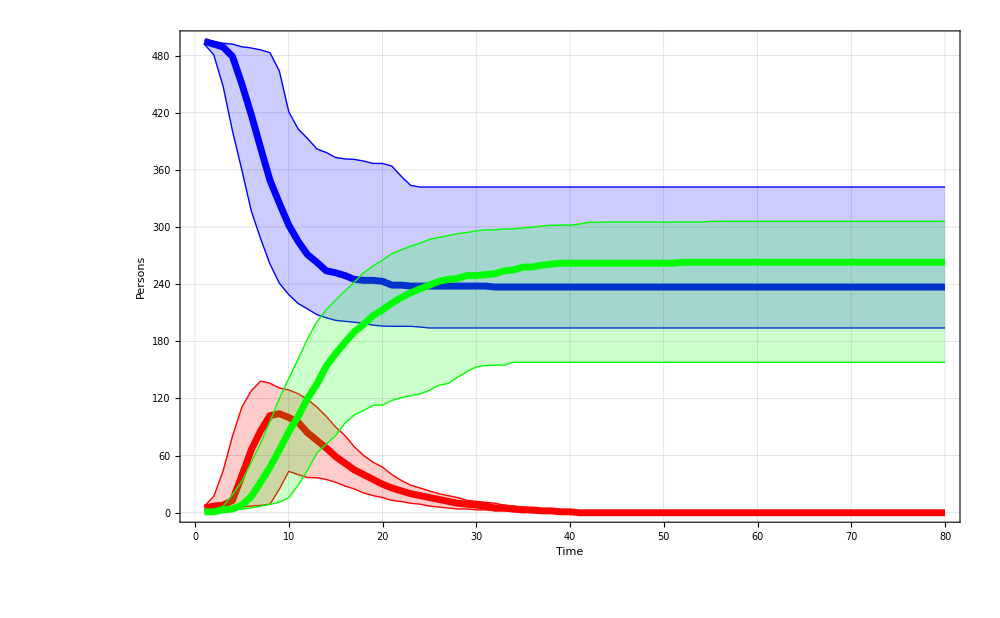
-Graphics- | -Graphics- |

BarabasiGrid.png

```mathematica
barabasiGrid=Grid[{{networkBarabasi//Show[#,ImageSize->800]&,quartilesBarabasi}}]
Export["BarabasiGrid.png",%]
```

### Watts

```mathematica
{tMin,tMax}={1,80};
fileNames=FileNames["*.csv",{NotebookDirectory[]<>"/Watts"}];
dataset=ParallelMap[InterpolateSIRFunctionsFromData[#]&,fileNames];
quartiles=CalculateSIRQuartiles[dataset, {tMin,tMax}];
quartilesWatts=PlotQuartiles[quartiles,{Blue,Red,Green}];
```

```mathematica
rawData={#[[1]],#[[2]],1}&/@Import["Watts.csv"];
edges=Flatten[{ToString[#[[1]]]->ToString[#[[2]]]}&/@Transpose[{rawData[[All,1]],rawData[[All,2]]}]];
weights=Chop/@rawData[[All,3]];
adjacencyMatrix=ConvertEdgesListToAdjacencyMatrix[edges,weights];
edgeshape[e_,___]:={Arrowheads[{{.00,.5}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[{adjacencyMatrix[[1]]//UpperTriangularize,adjacencyMatrix[[2]]}, 10,VariableStyle->"LineColor",VertexLabelStyle->Opacity[0],LineThickness->.002,EdgeShapeFunction->edgeshape,VertexSize->3,ImageSize->2000];
networkWatts=Rasterize[%,Background->None]//ColorNegate;
```

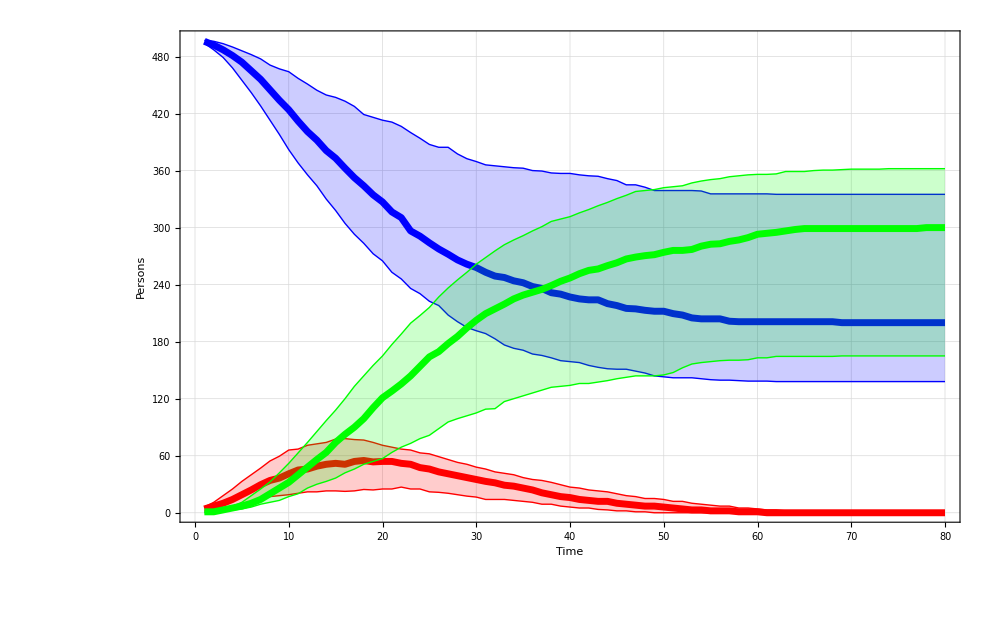
-Graphics- | -Graphics- |

WattsGrid.png

```mathematica
wattsGrid=Grid[{{networkWatts//Show[#,ImageSize->800]&,quartilesWatts}}]
Export["WattsGrid.png",%]
```

### Spatial

```mathematica
{tMin,tMax}={1,80};
fileNames=FileNames["*.csv",{NotebookDirectory[]<>"/Spatial"}];
dataset=ParallelMap[InterpolateSIRFunctionsFromData[#]&,fileNames];
quartiles=CalculateSIRQuartiles[dataset, {tMin,tMax}];
quartilesSpatial=PlotQuartiles[quartiles,{Blue,Red,Green}];
```

```mathematica
rawData={#[[1]],#[[2]],1}&/@Import["Spatial.csv"];
edges=Flatten[{ToString[#[[1]]]->ToString[#[[2]]]}&/@Transpose[{rawData[[All,1]],rawData[[All,2]]}]];
weights=Chop/@rawData[[All,3]];
adjacencyMatrix=ConvertEdgesListToAdjacencyMatrix[edges,weights];
edgeshape[e_,___]:={Arrowheads[{{.00,.5}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[{adjacencyMatrix[[1]]//UpperTriangularize,adjacencyMatrix[[2]]}, 10,VariableStyle->"LineColor",VertexLabelStyle->Opacity[0],LineThickness->.002,EdgeShapeFunction->edgeshape,VertexSize->6,ImageSize->2000];
networkSpatial=Rasterize[%,Background->None]//ColorNegate;
```

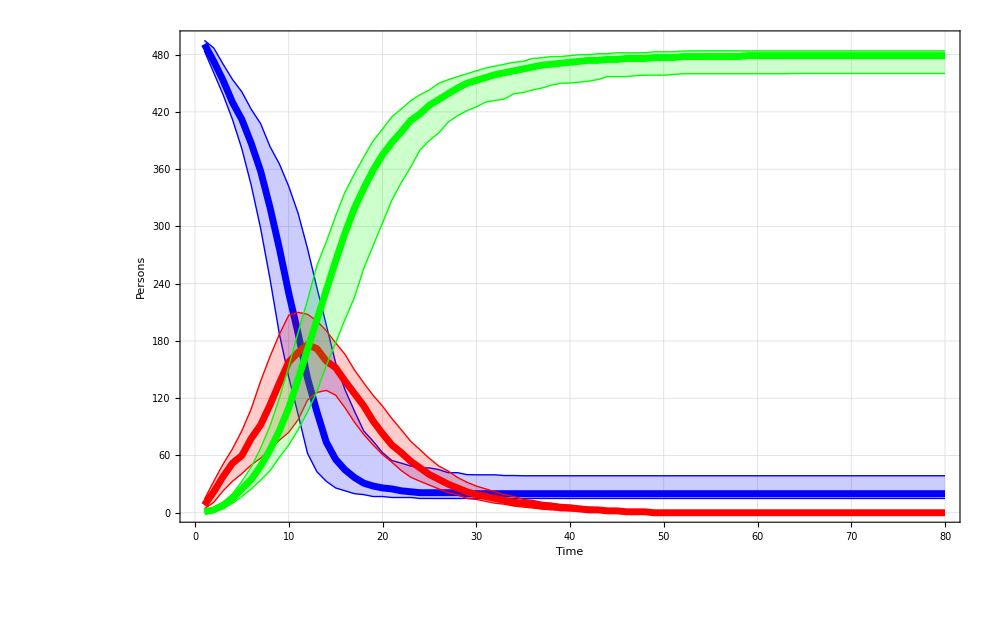
-Graphics- | -Graphics- |

SpatialGrid.png

```mathematica
spatialGrid=Grid[{{networkSpatial//Show[#,ImageSize->800]&,quartilesSpatial}}]
Export["SpatialGrid.png",%]
```

### Full

```mathematica
Grid[{
{barabasiGrid},
{wattsGrid},
{spatialGrid}
}];
Export["FullGrid.png",%]
```

FullGrid.png

```mathematica
Grid[{
Show[#,AspectRatio->1]&/@{quartilesBarabasi[[1,1,1]],quartilesWatts[[1,1,1]],quartilesSpatial[[1,1,1]]},
Show[#,ImageSize->600]&/@{networkBarabasi,networkWatts,networkSpatial}
}]
Export["FullGridQuartiles.png",%]
```

-Graphics-

FullGridQuartiles.png

## Networks Animations

These routines generate png frames to create an animation of a simulated epidemic. To create the final animation refer to the ‘ffmpeg.txt’ file.

### Export Graph

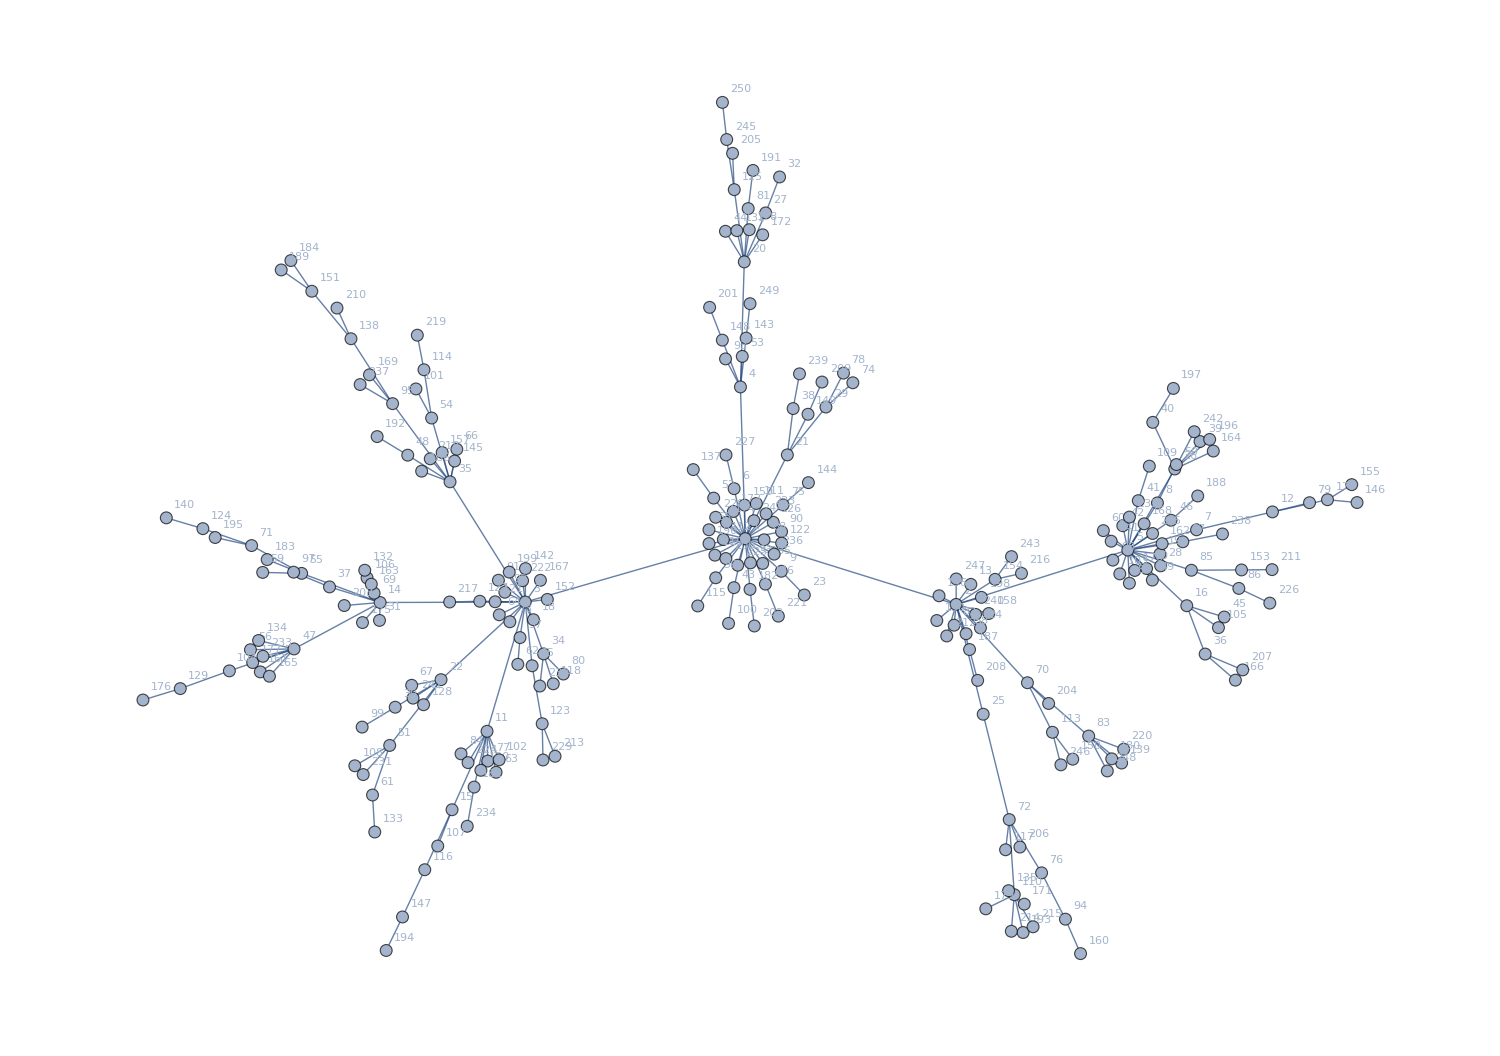

{{11.236,7.74802},{15.1699,6.52083},{7.13269,6.56501},{11.1468,10.5816},{18.3733,7.53541},{11.0286,8.68246},{19.6558,7.91402},{18.9263,8.41599},{11.9095,7.1391},{18.7236,7.19082},{6.4192,4.15144},{21.0719,8.24819},{15.4455,6.89487},{4.4252,6.5563},{5.7664,2.68675},{19.4732,6.49651},{22.0987,8.47558},{7.28549,6.23479},{18.9731,7.46128},{11.2181,12.9166},{12.0218,9.31277},{5.56111,5.11547},{12.3383,6.69637},{15.6242,6.08235},{15.6756,4.47012},{19.2499,9.04915},{11.6175,13.8313},{18.9866,7.24105},{12.7416,10.2061},{4.70615,4.60099},{4.41303,6.22181},{11.8767,14.5025},{11.334,7.29641},{7.4739,5.59664},{5.72923,8.80988},{19.8165,5.59356},{3.48058,6.84748},{12.1294,10.1775},{19.7206,9.56261},{18.839,9.9204},{18.5692,8.4579},{18.2797,7.99044},{11.0253,6.83378},{10.8671,13.488},{20.1723,6.2853},{19.1801,8.0918},{2.81905,5.68928},{4.93992,9.30725},{18.8311,6.97488},{19.2799,9.13246},{4.60344,3.88741},{10.6473,8.50565},{11.1809,11.1518},{5.38554,10.0009},{2.96039,7.10023},{2.00559,5.67428},{7.03454,5.90106},{15.3566,5.97348},{2.2338,7.1181},{17.9175,7.89849},{4.28276,2.96161},{6.99326,5.40199},{6.58791,3.38607},{6.64774,6.32656},{7.26028,5.37516},{5.85537,9.41667},{5.01327,5.01029},{10.5595,7.91455},{4.31252,6.73042},{16.5009,5.05825},{2.02696,7.61968},{16.1615,2.50274},{6.8454,6.1967},{13.2434,10.6597},{11.9422,8.37948},{16.7645,1.50813},{6.43227,3.59561},{13.0692,10.8396},{21.7631,8.42001},{7.84351,5.22028},{11.2911,13.9122},{15.1327,6.13272},{17.6433,4.06273},{5.93399,3.73051},{19.56,7.15849},{20.4447,6.81947},{19.4,7.69024},{11.5875,7.72715},{18.4029,6.91615},{11.9138,7.87862},{6.63181,6.9715},{6.75127,6.74789},{10.8686,11.1052},{17.2099,0.64289},{4.65725,10.2697},{10.6857,7.01817},{2.81088,7.12233},{18.0945,7.34771},{4.08912,4.22976},{10.9251,6.16587},{5.09276,10.5443},{6.64518,3.61911},{18.224,7.09102},{1.6125,5.2796},{20.0646,6.08717},{4.18114,7.01589},{5.49965,2.00896},{3.95243,3.50709},{18.7749,9.10223},{16.2559,1.09954},{11.4434,8.40572},{10.8282,7.73301},{16.9675,4.13295},{5.2426,10.9025},{10.3504,6.492},{5.25739,1.56671},{16.093,1.9391},{7.6552,5.03783},{10.6703,7.44016},{6.30425,3.42299},{6.57082,6.56998},{11.9152,7.66546},{7.44841,4.29267},{1.11818,7.93539},{11.0314,14.2655},{11.7594,8.05457},{6.2841,6.57959},{5.23528,4.64776},{0.696602,4.94851},{14.8101,6.21987},{11.0801,13.5},{4.13777,7.15864},{4.32453,2.27055},{2.1574,5.84676},{16.1484,1.17508},{11.6128,6.89942},{10.2663,9.03803},{3.88114,11.4814},{18.2576,3.55864},{0.435722,8.13709},{18.0633,7.70064},{7.13692,7.18933},{11.253,11.4933},{12.4148,8.79415},{5.81383,9.19764},{22.6501,8.42294},{4.84224,0.684446},{10.8093,11.455},{12.4073,10.0713},{17.346,3.63059},{3.15017,12.3685},{7.54426,6.61373},{20.4951,7.16465},{15.8969,6.98907},{22.5513,8.75704},{14.8515,6.68197},{5.58218,9.35667},{15.7792,6.35072},{11.224,8.37459},{17.4919,0.},{2.18964,5.2608},{19.0136,7.6553},{4.26019,6.89814},{19.9683,9.38418},{2.35984,5.17966},{20.3806,5.10636},{7.41501,6.97079},{18.6781,8.02593},{4.22541,10.8078},{18.5031,7.15472},{16.442,0.924084},{11.5614,13.4223},{11.0139,8.25596},{10.886,8.05333},{4.09566,6.18161},{0.,4.73564},{2.04741,5.43478},{11.3113,13.5177},{15.7242,0.836316},{18.0734,3.63713},{6.17823,3.10941},{11.3254,6.80108},{2.31754,7.35759},{2.75996,12.9414},{11.5623,7.28581},{5.19926,9.0087},{15.421,5.67809},{19.6779,8.54527},{2.57949,12.7662},{10.5606,7.65746},{11.3803,14.6244},{4.3692,9.65436},{16.4201,0.393975},{4.53796,0.0584771},{1.34758,7.76989},{19.9006,9.6015},{19.2237,10.5538},{15.6424,6.65239},{6.83367,7.1235},{10.8747,7.37765},{10.5714,12.0676},{11.4062,6.1178},{3.75541,6.49963},{16.8961,4.67068},{11.,14.9436},{16.3604,1.98981},{20.5173,5.29774},{15.5722,5.10226},{12.6677,10.6731},{3.61994,12.0542},{21.0647,7.17017},{14.9956,5.93162},{7.68807,3.68483},{16.2004,0.417258},{16.6062,0.500875},{16.3901,7.09991},{5.72185,6.56559},{5.36001,9.23919},{5.1186,11.5478},{18.2964,3.81674},{11.8541,6.30132},{7.08236,6.9635},{11.6254,8.21362},{6.06473,3.56668},{11.0962,7.25244},{21.0226,6.54479},{10.8777,9.31196},{10.6846,8.14777},{7.46344,3.6157},{7.40381,4.99614},{4.10911,3.34353},{18.4031,8.15137},{2.23914,5.55172},{6.04978,2.37795},{18.8355,7.84495},{11.7754,7.45929},{4.05187,10.6262},{20.1398,7.83593},{12.2486,10.826},{15.5331,6.33431},{5.03884,4.77038},{19.6123,9.74516},{16.2036,7.41319},{11.3977,8.08382},{10.8903,15.2014},{17.1251,3.52508},{15.1724,6.99623},{17.9909,3.41088},{11.3258,12.1361},{10.811,15.895}}

BA.csv

BACoords.csv

```mathematica
n=250;
randomGraph=RandomGraph[BarabasiAlbertGraphDistribution[n,1],ImageSize->1500,VertexLabels->"Name",VertexSize->2.5]

edgesList=GraphIntoEdgesList[randomGraph];
coords=GraphEmbedding[randomGraph]
Export["BA.csv",Cases[edgesList,{a_,b_,1.}->{a,b}]]
Export["BACoords.csv",coords]
```

### Import

```mathematica
SetDirectory[NotebookDirectory[]];
{NAValue,timeScaling ,colours,imageSize,indexCase,name}={60,50,{Blue,Red,Green},2000,2,"twitter"};
range={1,NAValue*timeScaling};
{scaledHistory,sortedEvents}=ImportHistory[name<>"History.csv",timeScaling,NAValue];
(*coordinates=ToExpression/@Import[name<>"Coords.csv"];*)
colourFrames=CreateFramesColorList[scaledHistory,sortedEvents,colours];
colourEdges=CreateFramesEdgeColorList[scaledHistory,sortedEvents,{Lighter[Black,.7],Directive[Purple,Thickness[.005]]}];
(*Network*)
rawData={#[[1]],#[[2]],1}&/@Import[name<>".csv"];
{edges,weights}={Flatten[{ToString[#[[1]]]->ToString[#[[2]]]}&/@Transpose[{rawData[[All,1]],rawData[[All,2]]}]],Chop/@rawData[[All,3]]};
adjacencyMatrix=ConvertEdgesListToAdjacencyMatrix[edges,weights];
```

### Networks

```mathematica
edgeshape[e_,___]:={Arrowheads[{{.00,.5}}],Arrow[e]}
graphs=ParallelMap[
GraphTransitionsFrequenciesWithMax[{adjacencyMatrix[[1]]//UpperTriangularize,adjacencyMatrix[[2]]}, 5,
VariableStyle->"None",
VertexLabelStyle->Opacity[0],
GraphLayout->"RadialEmbedding",
(*VertexCoordinates->coordinates[[ToExpression/@adjacencyMatrix[[2]]]],*)
LineThickness->.005,
EdgeShapeFunction->edgeshape,
VertexSize->7.5,
ImageSize->{imageSize,imageSize},
EdgeStyle->Flatten[{#[[1,1]]<->#[[1,2]]->#[[2]],#[[1,2]]<->#[[1,1]]->#[[2]]}&/@#[[2]]],
BaseStyle->Directive[Lighter[Black,.7],Thickness[.001],Opacity[.9],EdgeForm[Directive[Black,Opacity[1],Thickness[.0025]]]],
VertexStyle->((ToString [#[[1]]]->#[[2]])&/@#[[1]])]&
,Transpose[{colourFrames[[range[[1]];;range[[2]]]],colourEdges[[range[[1]];;range[[2]]]]}]
];
```

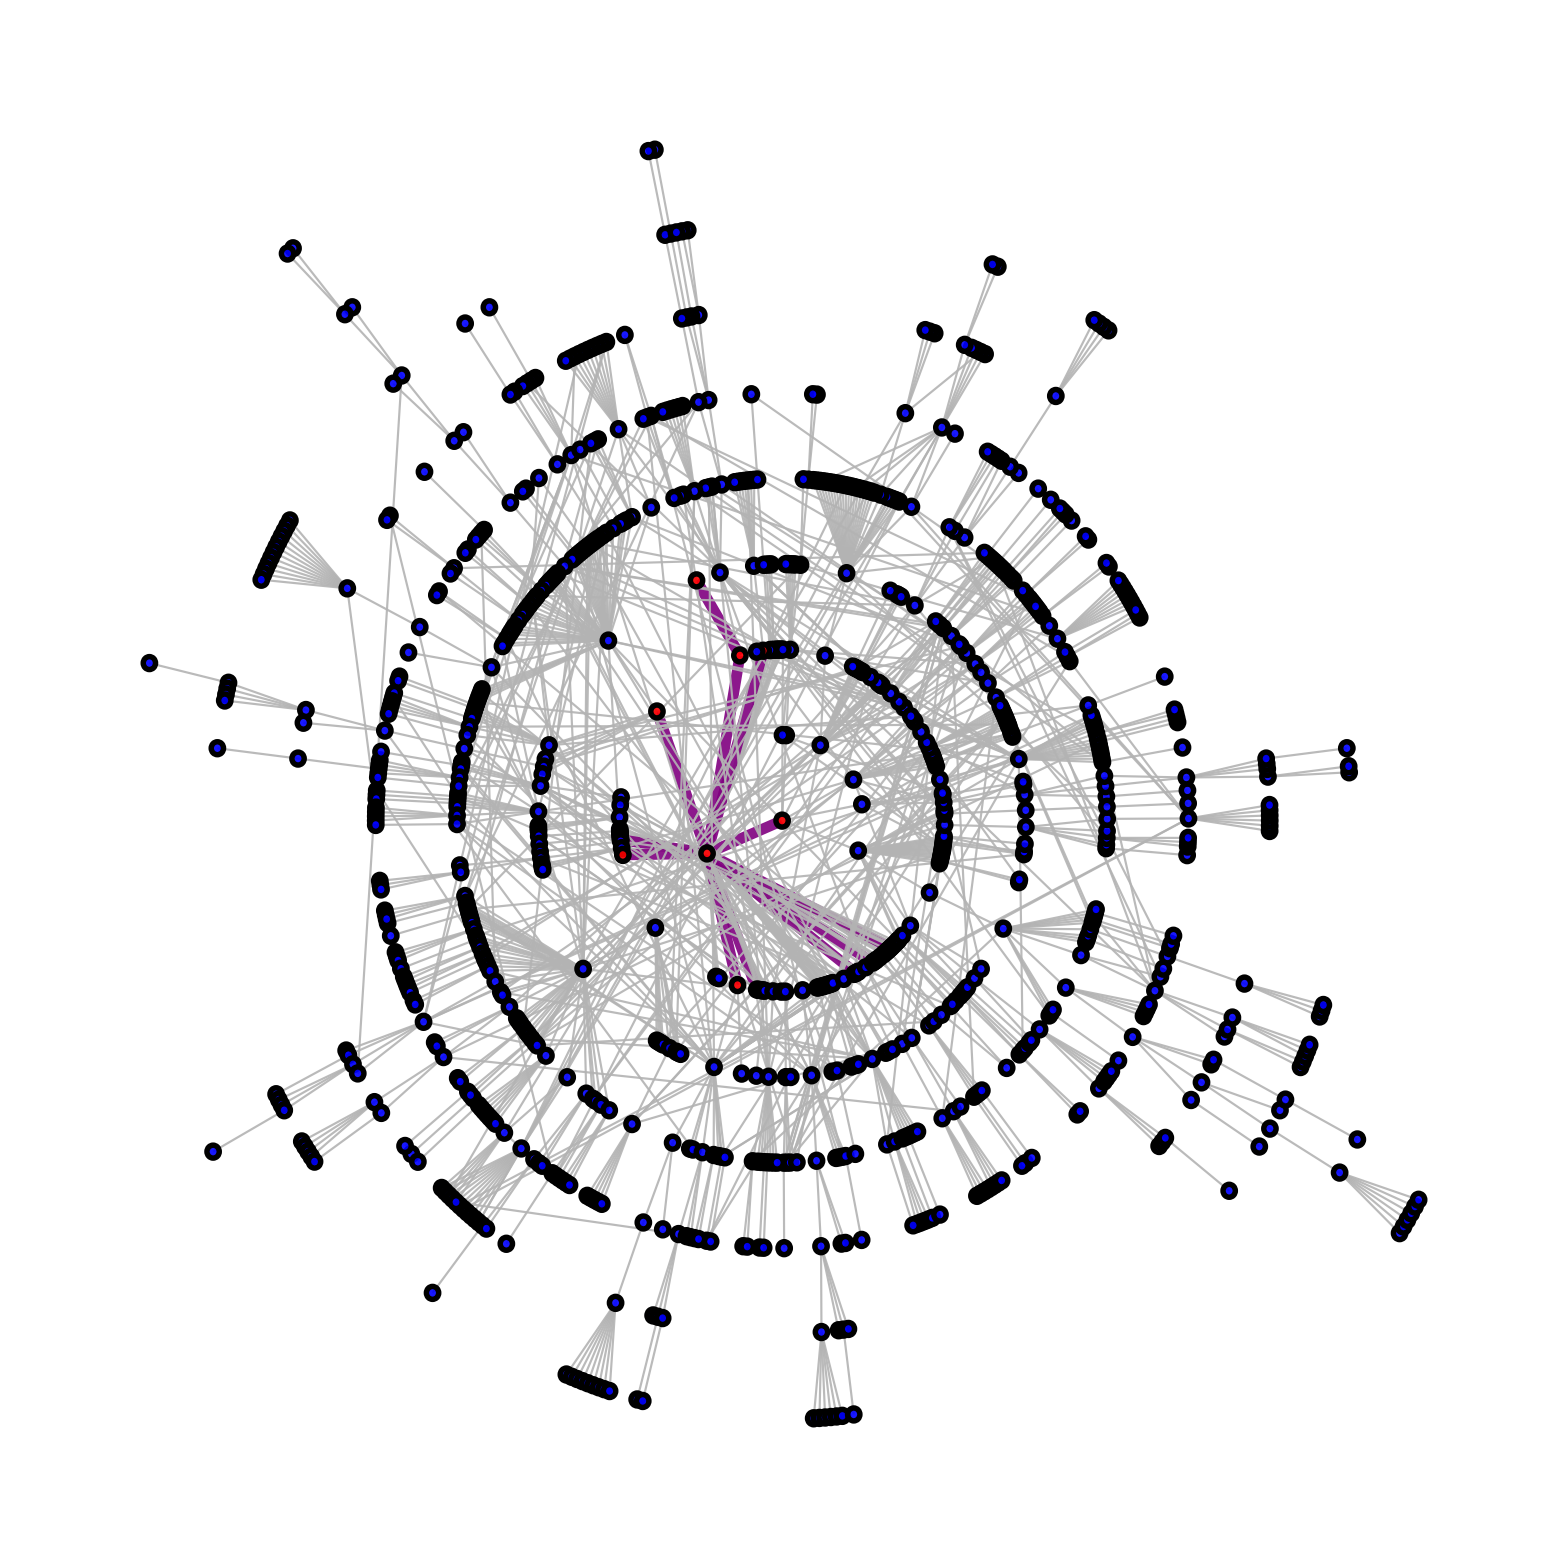

```mathematica
graphs[[100]]
```

### Lines Bar Chart

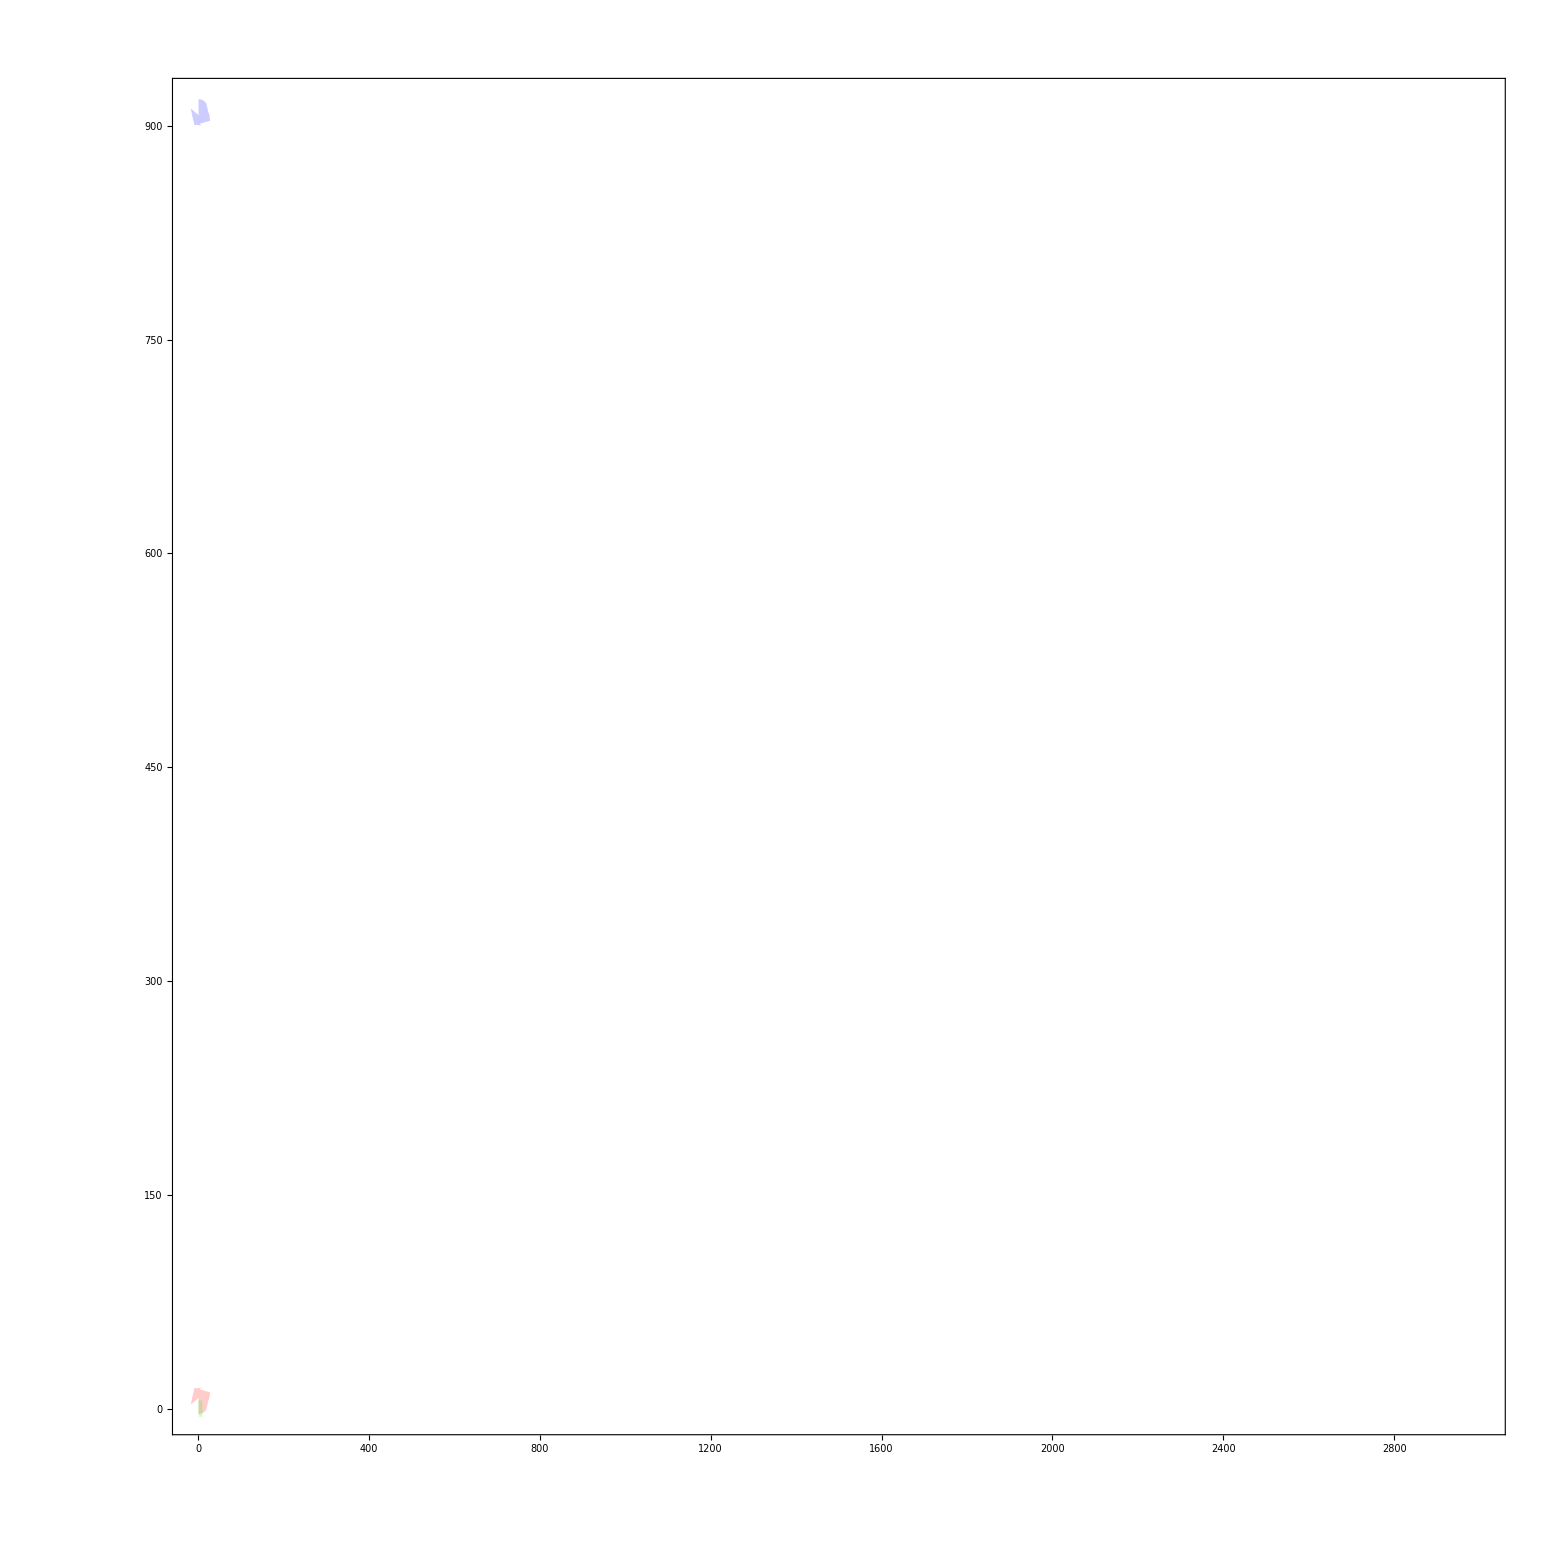

```mathematica
sirCounts={Count[#[[All,2]],Blue],Count[#[[All,2]],Red],Count[#[[All,2]],Green]}&/@(colourFrames[[range[[1]];;range[[2]]]]);
timedTuples={Range[range[[1]],range[[2]]],sirCounts}//Transpose;
coordinates={{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]},{#[[1]],#[[2,3]]}}&/@timedTuples;
listLines=
ParallelTable[
ListLinePlot[
coordinates[[1;;i]]//Transpose
,PlotStyle->{Directive[Blue,Opacity[.2],Thickness[.0075]],Directive[Red,Opacity[.2],Thickness[.0075]],Directive[Green,Opacity[.2],Thickness[.0075]]}
,PlotRange->{{0,timeScaling*NAValue},{0,adjacencyMatrix[[2]]//Length}}
,GridLines->None
,GridLinesStyle->Directive[{Gray,Thickness[.005],Opacity[0]}]
,BaseStyle->40
,Frame->True
,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]
,FrameStyle->Directive[{Gray,Thickness[.03]}]
(*,FrameLabel->(Style[#,40]&/@{"Time","Persons"})*)
,ImageSize->{imageSize,imageSize}
,AspectRatio->1
,InterpolationOrder->1
,ImagePadding->None
,Prolog->Inset[
BarChart[
coordinates[[i,All,2]]
,BaseStyle->Directive[Opacity[.25]]
,ChartStyle->{
Directive[Blue,EdgeForm[Directive[Thickness[.005],Opacity[0]]]],
Directive[Red,EdgeForm[Directive[Thickness[.005],Opacity[0]]]],
Directive[Green,EdgeForm[Directive[Thickness[.005],Opacity[0]]]]
}
,ChartLayout->"Percentile"
,Axes->None
,AspectRatio->1
,ImageSize->{imageSize*1.06,imageSize*2}
(*,ChartLegends->Placed[Style[#,25,Bold,Gray]&/@{"S","I","R"},Top]*)
]
,{imageSize*2.1(*490*),475}](*{(colourFrames//Length)*.8965,(adjacencyMatrix[[2]]//Length)*.9015}]*)
]
,{i,1,sirCounts//Length}];
listLines[[10]]
```

### Test

```mathematica
testPoint=100;
Show[
Rasterize[listLines[[testPoint]]],
Rasterize[graphs[[testPoint]],Background->None]
]
```

### Export

```mathematica
Table[
Export[NotebookDirectory[]<>"Frames/"<>StringPadLeft[ToString[i],4,"0"]<>".png",
Show[Rasterize[listLines[[i]]],Rasterize[graphs[[i]],Background->None]]
]
,{i,1,timeScaling*NAValue-1}];
```